# General Relativistic Vorticity Solver

Quick scan parameters
Conserved canonical momentum associated with ϕ and t Lagrangian independence (constants of motion)
Tweak number to chose different solutions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
Eomc=1.1;J=0.0;
LomMin=4;LomMax=5;dLom=0.01;
tweak=2;
```

## Input Parameters

## Metric

### Available metrics

```mathematica
ggschwarz = { {  1-rs/r,   0         ,      0       ,     0                         },
          {     0         , - 1/(1-rs/r),      0       ,     0                         },
          {     0         ,     0       ,      -r^2     ,     0                        },
          {     0         ,     0       ,      0       , -r^2 Sin[θ]^2  }};
ggminkowski={ {  1,   0         ,      0       ,     0                         },
          {     0         , -1,      0       ,     0                         },
          {     0         ,     0       ,      -1     ,     0                        },
          {     0         ,     0       ,      0       , -1  }};
ggFLRW={ {  1,   0         ,      0       ,     0                         },
          {     0         , - a[t]^2/(1-k r^2),      0       ,     0                         },
          {     0         ,     0       ,      -a[t]^2 r^2     ,     0                        },
          {     0         ,     0       ,      0       , -a[t]^2 r^2 Sin[θ]^2  }};
a[t_]=Exp[0.1 t];k=0;
ggKerr={ {  1-(rs r)/ρ2        ,   0      ,     0   , rs r α Sin[θ]^2     },
          {     0                       , - ρ2/Δ   ,    0   ,       0                         },
          {     0                       ,     0      , -ρ2  ,      0                          },
          { rs r α Sin[θ]^2,     0     , 0       , -(r^2+α^2+(rs r α^2)/ρ2 Sin[θ]^2)Sin[θ]^2  }};
rs=2m;α=J/m;ρ2=r^2+α^2 Cos[θ]^2;Δ=r^2-rs r+α^2;
```

### Choose input metric/coordinate

```mathematica
gg=ggKerr;
d = 4;
xx = {t,r,θ,ϕ};
```

#### Allocate arrays used later

```mathematica
xxVorsphe=xx /.t->t[τ]/.r->r[τ]/.θ->θ[τ]/.ϕ->ϕ[τ];
xxtsphe=xx /.r->r[τ]/.θ->θ[τ]/.ϕ->ϕ[τ];
xxVor=xxVorsphe;
xxt=xxtsphe;
```

## Physical Parameters

### Initial Conditions

Initial radius, θ, θ’, τ and maximum τ
Set Lagrangian = -1,0,1 depending on timelike, lightlike or spacelike test particle

```mathematica
motionconstant={Eomc,LomMin};
τmin=0;τmax=300;rmax=7rs;ϕ0=0;θprime0=0;
lagrangian=1;
```

### BH parameters

```mathematica
stoprs=True;(*Stop the particle at Schwarzschild radius*)
m=1;
rs=2m;
```

### Number of spline steps

```mathematica
nsteps=10000;
```

### Magnetofluid parameters

Charge, χ and temperature radial dependence

```mathematica
χ=1;q=1;c=1;temperature[r_]=((1-√(rs/r))/r^3)^(1/4);
```

## Geodesic

## Lagrangian Equations

### Metric, Lagrangian (TT) and canonical moments

```mathematica
Do[g[i,j]=gg[[i,j]]/.Table[xx[[i]]->xxVor[[i]],{i,1,d}],{i,1,d},{j,1,d}];
TT=Sum[g[i,j]D[xxVor[[i]],τ]D[xxVor[[j]],τ],{i,1,d},{j,1,d}];
moments=Table[D[TT,xxVor[[i]]],{i,1,d}];
```

## Initial Conditions/Evaluation Options

### Read from input parameters

```mathematica
InConds={t[0]==0,r[0]==rmax,ϕ[0]==ϕ0,θ[0]==Pi/2,θ'[0]==θprime0};
```

### Stop evaluation when r starts to be imaginary, bigger than initial radius or enters r_Schwarzschild

```mathematica
If[stoprs==True,
whenevent={WhenEvent[ {Im[r[τ]]>10^-40,Abs[r[τ]]==1.001(rs+√(rs^2-4 α^2))/2,Abs[r[τ]]>1.01rmax},{"StopIntegration",ττmax=0.9999N[τ,8]},"LocationMethod"->{"Brent",AccuracyGoal->8,PrecisionGoal->8},"IntegrateEvent"->False]},
whenevent={WhenEvent[ {Im[r[τ]]>10^-40,Abs[r[τ]]>10^5},{"StopIntegration",ττmax=0.9999N[τ,8]},"LocationMethod"->{"Brent",AccuracyGoal->8,PrecisionGoal->8},"IntegrateEvent"->False]}];
```

## Solve Geodesic PDE’s

Here, we will find for the best stable/physical orbit. This means that we are looking for an orbit that decreases it’s radius as a function of time, travels a long time before arriving at the BH and is physical: has no imaginary parts, increasing time and increasing ϕ

### Define Function - Obtain solution as a function of the initial equations/constants of motion

```mathematica
geosolution:=(
(*Obtain Euler-Lagrange equations or use conserved momentum*)
tt=1;
Geo1=Table[0,{i,1,d}];
For[i=1,i≤d,i++,
If[Flatten[Internal`RealValuedNumericQ/@{moments[[i]]}][[1]],
Geo1[[i]]={D[TT,D[xxVor[[i]],τ]]==2motionconstant[[tt]]}[[1]];tt++,
Geo1[[i]]={D[D[TT,D[xxVor[[i]],τ]],τ]==D[TT,xxVor[[i]]]}[[1]]]];
eqs=ReplacePart[Geo1,2->TT==lagrangian];
(*Solve differential equations*)
sol=NDSolve[{eqs,InConds,whenevent},xxVor,{τ,τmin,τmax},MaxStepFraction->1/1000,Method->{"EquationSimplification"->"Residual"}];
(*Choose increasing time, real radius, decreasing radius, increasing ϕ*)
solnumber=If[stoprs==True,
Intersection[Flatten[Position[t[τ]/.sol/.τ->ττmax,_?(#>0&)]],
Flatten[Position[r[τ]/.sol/.τ->ττmax,_?(Im[#]==0&)]],
Flatten[Position[r[τ]/.sol/.τ->ττmax/2,_?(#<1.01rmax&)]],
Flatten[Position[ϕ[τ]/.sol/.τ->ττmax,_?(#<=ϕ[τ]/.sol[[1]]/.τ->0&)]]][[1]],
Intersection[Flatten[Position[t[τ]/.sol/.τ->ττmax,_?(#>0&)]],
Flatten[Position[r[τ]/.sol/.τ->ττmax,_?(Im[#]==0&)]],
Flatten[Position[r[τ]/.sol/.τ->ττmax/2,_?(#>=rmax&)]],
Flatten[Position[ϕ[τ]/.sol/.τ->ττmax,_?(#<=ϕ[τ]/.sol[[1]]/.τ->0&)]]][[1]]];
)
```

### Change constants of motion to have best stable/physical orbit

Through this change, solve the system many times trying to maximize the total travel time within physical orbits
Save list of good initial conditions in LomSolutions and print it, together with the maximum found time (commented out)

```mathematica
Lom=LomMin;
LomSolutions={};
Quiet[geosolution]
tmax1=ττmax;t0=τmax;tmin=20;tmin1=20;
Monitor[
While[
Lom<LomMax,
Lom1=Lom;
While[
ττmax<=t0 ||ττmax≤tmin||Quiet[FindMinimum[{Abs[r[τ]/.sol/.sol[[solnumber]]][[1]],τmin<τ<0.99ττmax},{τ,ττmax}][[1]]≥0.8 rmax],
t0=ττmax;Lom+=dLom;motionconstant={Eomc,Lom};(*Print[{Lom}];*)
Quiet[geosolution];If[Lom≥LomMax,Break[]];
];
tmin1=tmin;tmin=1.1ττmax;LomSolutions=Append[LomSolutions,Lom1];Print[{Lom1,tmin1}];
],
Row[{ProgressIndicator[Lom,{LomMin,LomMax}],Lom}," "]
]
```

{4,20}

{4.01,25.2741}

{4.33,27.8857}

{4.52,30.6791}

{4.63,33.8077}

{4.69,37.6936}

{4.72,45.1738}

{4.73,71.2714}

## Solve for the best solution

There is the freedom to choose from a number of solutions. This is a tweak parameter to provide different stable orbits

```mathematica
Lom=Take[LomSolutions,-tweak][[1]];
motionconstant={Eomc,Lom}
geosolution;
```

{1.1,4.72}

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

## Vorticity Generation

## Array Interpolation

Create table of interpolated arrays to easily derive/integrate with built-in functions

### t, r, ϕ and θ arrays

```mathematica
toftautemp=Table[{τ,Re[t[τ]]/.sol[[solnumber]]}/.τ->tt,{tt,τmin,ττmax,(ττmax-τmin)/nsteps}];
toftau=Interpolation[toftautemp,Method->"Spline"];
roftautemp=Table[{τ,Re[r[τ]]/.sol[[solnumber]]}/.τ->tt,{tt,τmin,ττmax,(ττmax-τmin)/nsteps}];
roftau=Interpolation[roftautemp,Method->"Spline"];
rofttemp=Table[{Re[t[τ]]/.sol[[solnumber]],Re[r[τ]]/.sol[[solnumber]]}/.τ->tt,{tt,τmin,ττmax,(ττmax-τmin)/nsteps}];
roft=Interpolation[rofttemp,Method->"Spline"];
θofttemp=Table[{Re[t[τ]]/.sol[[solnumber]],Re[θ[τ]]/.sol[[solnumber]]}/.τ->tt,{tt,τmin,ττmax,(ττmax-τmin)/nsteps}];
θoft=Interpolation[ϕofttemp,Method->"Spline"];
ϕoftautemp=Table[{τ,Re[ϕ[τ]]/.sol[[solnumber]]}/.τ->tt,{tt,τmin,ττmax,(ττmax-τmin)/nsteps}];
ϕoftau=Interpolation[ϕofttemp,Method->"Spline"];
ϕofttemp=Table[{Re[t[τ]]/.sol[[solnumber]],Re[ϕ[τ]]/.sol[[solnumber]]}/.τ->tt,{tt,τmin,ττmax,(ττmax-τmin)/nsteps}];
ϕoft=Interpolation[ϕofttemp,Method->"Spline"];
rofϕtemp=Table[{Re[ϕ[τ]]/.sol[[solnumber]],Re[r[τ]]/.sol[[solnumber]]}/.τ->tt,{tt,τmin,ττmax,(ττmax-τmin)/nsteps}];
rofϕ=Interpolation[rofϕtemp,Method->"Spline"];
```

Interpolation::innd: First argument in ϕofttemp does not contain a list of data and coordinates.

### Velocity, metric and Lorentz factor as a function of t, dr/dϕ(r)

```mathematica
tmin=toftau[τmin];
tmax=toftau[ττmax];
velocityvector[t_]={1,roft'[t],θoft'[t],ϕoft'[t]};
metricoft[t_]=gg/.r->roft[t]/.θ->θoft[t]/.ϕ->ϕoft[t];
drdϕ[ϕ_]=D[rofϕ[ϕ],ϕ];
drdϕofrtemp=Table[{Re[rofϕ[ϕ]],Re[drdϕ[ϕ]]},{ϕ,Min[ϕoftau[τmin],ϕoftau[ττmax]],Max[ϕoftau[τmin],ϕoftau[ττmax]],(ττmax-τmin)/nsteps}];
drdϕofr=Interpolation[drdϕofrtemp,Method->"Spline"];
```

## Lorentz factor (as a function of time and radius)

```mathematica
Γoft[t_]=√(1/Sum[metricoft[t][[i,j]]velocityvector[t][[i]]velocityvector[t][[j]],{i,1,d},{j,1,d}]);
Γofrtemp1=Table[{roftau[τ],toftau'[τ]},{τ,τmin,ττmax,(ττmax-τmin)/nsteps}];
Γofrtemp2=Table[{roft[t],Γoft[t]},{t,tmin,tmax,(tmax-tmin)/nsteps}];
Γofr1=Interpolation[Γofrtemp1,Method->"Spline"];
Γofr2=Interpolation[Abs[Γofrtemp2],Method->"Spline"];
```

## Vorticity

```mathematica
Ω[r_]=(c χ/q)/(√(gg[[2,2]]gg[[4,4]]/.θ->π/2))D[1/Γofr1[r],r]D[temperature[r],r]drdϕofr[r];
```

## Figures

## General Plot Options

```mathematica
PlotOptions=Flatten[{PlotRange->Full,ImageSize->Medium,AspectRatio->1/1.3,PlotStyle->Thickness[0.007]}];
PlotOptions2=Flatten[{PlotLabel->"",LabelStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->15],Frame->False,ImageSize->600}];
TickScale[plotname_,factor_]:=Map[Times[#,{1,If[NumberQ[#[[2]]],1/factor,1],{1,1},{1,1}}]&,AbsoluteOptions[plotname,Ticks][[1,2,1]]];
```

## Black Hole (r_Schwarzschild) + Orbit

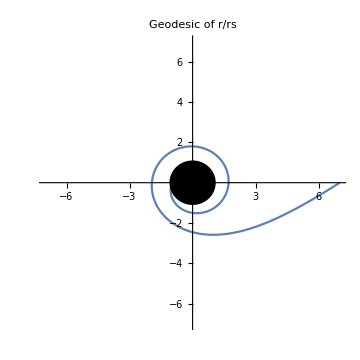

```mathematica
BHplot=ParametricPlot[{ Cos[u], Sin[u]},{u,0,2 Pi}]/.Line[l_List]:>{{Black,Polygon[l]},{Directive[AbsoluteThickness[3],Black],Line[l]}};
orbitbh=Show[ParametricPlot[{Re[r[τ]/rs]Re[Cos[ϕ[τ]]],Re[r[τ]/rs]Re[Sin[ϕ[τ]]]}/.sol[[solnumber]],{τ,τmin,ττmax},PlotRange->rmax/rs,PlotLabel->"Geodesic of r/rs",ImageSize->Medium],BHplot]
```

## Grid of All Figures

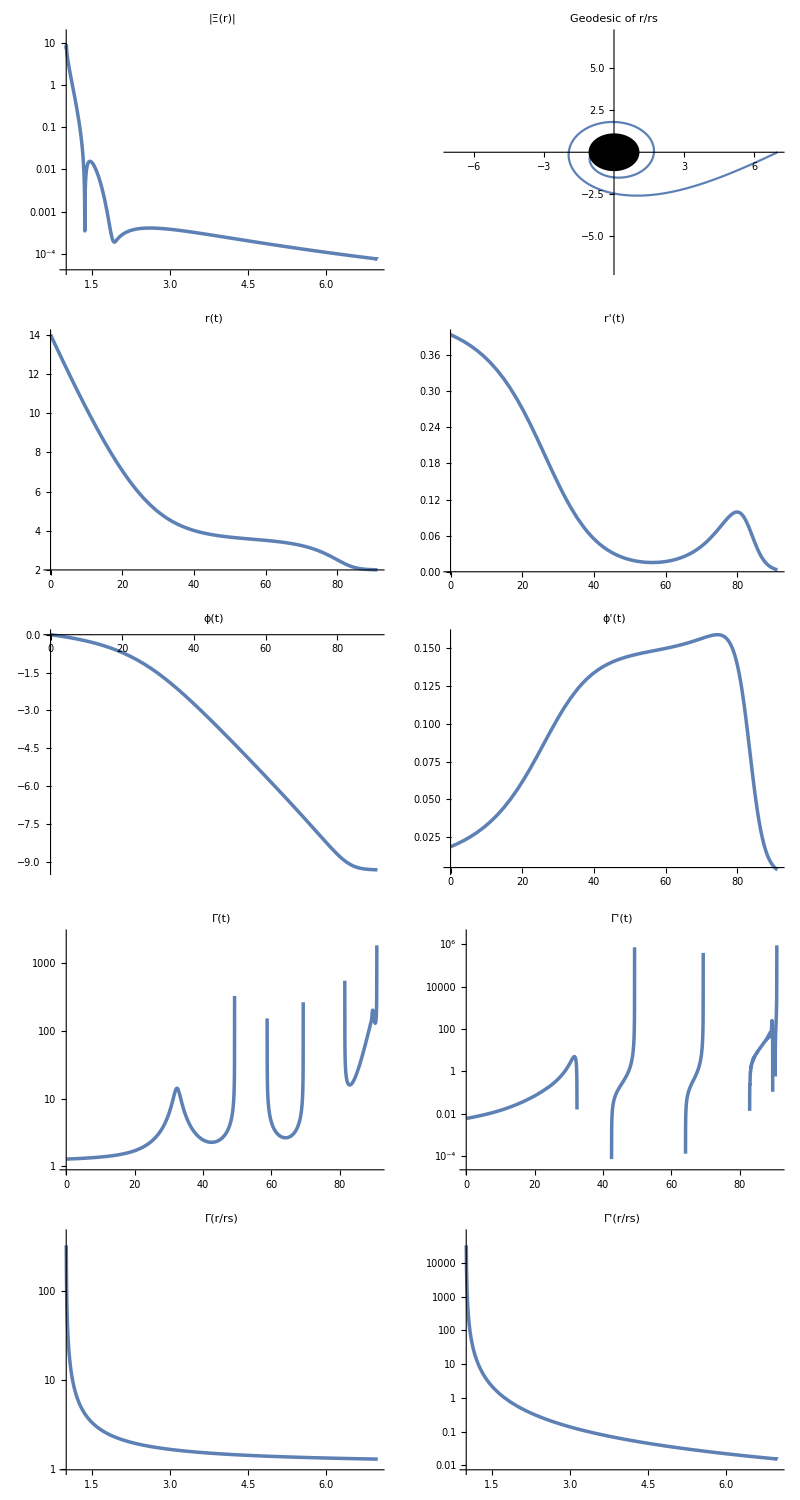

```mathematica
Grid[{
If[stoprs==True,
{vort=LogPlot[Abs[Ω[r rs]],{r,roftau[ττmax]/rs,rmax/rs},PlotLabel->"|Ξ(r)|",Evaluate@PlotOptions],orbitbh},
{ContourPlot[Abs[Ω[r rs]]/.t->tt,{r,roftau[ττmax]/rs,rmax/rs},{tt,toftau[τmin],toftau[ττmax]},PlotLabel->"Ω(r/rs)",Evaluate@PlotOptions],ParametricPlot3D[{Re[r[τ]/rs]Re[Cos[ϕ[τ]]]Re[Cos[θ[τ]]],Re[r[τ]/rs]Re[Sin[ϕ[τ]]]Re[Cos[θ[τ]]],Re[r[τ]/rs]Re[Sin[θ[τ]]]}/.sol[[solnumber]],{τ,τmin,ττmax},PlotLabel->"Geodesic of r/rs",Evaluate@PlotOptions]}],
{Plot[roft[t],{t,tmin,tmax},PlotLabel->"r(t)",Evaluate@PlotOptions],
roftd=Plot[Abs[roft'[t]],{t,tmin,tmax},PlotLabel->"r'(t)",Evaluate@PlotOptions]},
{Plot[ϕoft[t],{t,tmin,tmax},PlotLabel->"ϕ(t)",Evaluate@PlotOptions],
ϕoftd=Plot[Abs[ϕoft'[t]],{t,tmin,tmax},PlotLabel->"ϕ'(t)",Evaluate@PlotOptions]},
{Γoft1=LogPlot[Γoft[t],{t,tmin,tmax},PlotLabel->"Γ(t)",Evaluate@PlotOptions],
Γoft1d=LogPlot[Γoft'[t],{t,tmin,tmax},PlotLabel->"Γ'(t)",Evaluate@PlotOptions]},
{Γofr12=LogPlot[Abs[Γofr1[r rs]],{r,roftau[ττmax]/rs,rmax/rs},PlotLabel->"Γ(r/rs)",Evaluate@PlotOptions],
Γofr12d=LogPlot[Abs[Γofr1'[r rs]],{r,roftau[ττmax]/rs,rmax/rs},PlotLabel->"Γ'(r/rs)",Evaluate@PlotOptions]}
},Frame->All]
```

## Movie

Takes a long time, commented by default

```mathematica
(*geo1=Table[Show[ParametricPlot[{Re[r[τ]/rs]Re[Cos[ϕ[τ]]],Re[r[τ]/rs]Re[Sin[ϕ[τ]]]}/.sol[[solnumber]],{τ,τmin,ttt},PlotRange->rmax,PlotLabel->Style["Geodesic of r/rs",FontFamily->"Adobe Caslon Pro",FontSize->40],LabelStyle->Directive[FontFamily->"Adobe Caslon Pro",FontSize->35],Frame->True,FrameLabel->{"x/r_s","y/r_s"},ImageSize->1000,PlotStyle->Directive[RGBColor[0.18,0.42,0.87],Thickness[0.005]]],BHplot],{ttt,0.1,ττmax,0.05}];
Export["images/geo1_rs"<>parameterstring<>".swf",geo1,"FrameRate"->35];*)
```

## Publication Ready Plots

```mathematica
roftds=Show[roftd,AxesLabel->{"t","v^r"},Evaluate@PlotOptions2];
ϕoftds=Show[ϕoftd,AxesLabel->{"t","v^ϕ"},Evaluate@PlotOptions2];
Γoft1s=Show[Γoft1,AxesLabel->{"t","Γ"},Evaluate@PlotOptions2];
Γoft1ds=Show[Γoft1d,AxesLabel->{"t","Γ'"},Evaluate@PlotOptions2];
Γofr12s=Show[Γofr12,AxesLabel->{"r/r_s","Γ"},Evaluate@PlotOptions2];
Γofr12ds=Show[Γofr12d,AxesLabel->{"r/r_s","Γ'"},Evaluate@PlotOptions2];
vorts=Show[vort,AxesLabel->{"r/r_s","|Ω| a.u."},Evaluate@PlotOptions2];
```

## Save Data

## File Saving Path/Extension

```mathematica
SetDirectory[NotebookDirectory[]];
imagepath="images/";
resultspath="results/";
parameterstring=StringReplace["rs"<>ToString[rs]<>"rmax"<>ToString[rmax]<>"thetaprime0"<>ToString[θprime0]<>"Lom"<>ToString[Lom]<>"Eomc"<>ToString[Eomc]<>"J"<>ToString[J],"."->"-"];
filextension="dat";
```

## Save Plots

```mathematica
Export[imagepath<>"roftd"<>parameterstring<>".pdf",roftds];
Export[imagepath<>"phioftd"<>parameterstring<>".pdf",ϕoftds];
Export[imagepath<>"gammaoft"<>parameterstring<>".pdf",Γoft1s];
Export[imagepath<>"gammaoftd"<>parameterstring<>".pdf",Γoft1ds];
Export[imagepath<>"gammaofr"<>parameterstring<>".pdf",Γofr12s];
Export[imagepath<>"gammaofrd"<>parameterstring<>".pdf",Γofr12ds];
Export[imagepath<>"vort"<>parameterstring<>".pdf",vorts];
```

## Save Physical Quantities

```mathematica
toftau[τ]>>resultspath<>parameterstring<>"toftau."<>filextension
roftau[τ]>>resultspath<>parameterstring<>"roftau."<>filextension
roft[t]>>resultspath<>parameterstring<>"roft."<>filextension
θoft[t]>>resultspath<>parameterstring<>"thetaoft."<>filextension
ϕoft[t]>>resultspath<>parameterstring<>"phioft."<>filextension
velocityvector[t]>>resultspath<>parameterstring<>"velocityvector."<>filextension
metricoft[t]>>resultspath<>parameterstring<>"metricoft."<>filextension
Γoft[t]>>resultspath<>parameterstring<>"gammaoft."<>filextension
Γofr1[r rs]>>resultspath<>parameterstring<>"gammaofr."<>filextension
Ω[r rs]>>resultspath<>parameterstring<>"vorticity."<>filextension
```

## Parameter Scan

## Variation with J

### Sort data

```mathematica
vorticityfiles=FileNames["*vorticity*",{"results"}];
nfiles=Length[vorticityfiles];
legendJtemp=Table[
StringReplace[
StringReplace[
StringReplace[
StringReplace[
vorticityfiles[[i]],StringTake[vorticityfiles[[i]],Take[StringPosition[vorticityfiles,"E"]//Flatten,{1,-1,2}][[i]]-1]->""
],
{"-"->".","vorticity."<>filextension->"","Eomc"->"E/mc^2=","J0"->"a=0","Lom"->"L/m="}
],
{".a"->".0 a"}
],
{"a"->", a"}
],
{i,1,nfiles}
];
legendJ=Sort[legendJtemp]
ordering=Flatten[Table[Position[legendJtemp,_?(#==legendJ[[i]]&)],{i,1,nfiles}]];
```

{E/mc^2=1.0 , a=0.,E/mc^2=1.0 , a=0.5,E/mc^2=1.0 , a=0.8,E/mc^2=1.0 , a=0.99,E/mc^2=1.1, a=0.,E/mc^2=1.5, a=0.,E/mc^2=1.5, a=0.5,E/mc^2=1.5, a=0.8,E/mc^2=1.5, a=0.99}

### Retrieve and sort data

```mathematica
vorticityfiles=FileNames["*vorticity*",{"results"}];
vorticitydata1=Table[Get[vorticityfiles[[i]]],{i,1,nfiles}];
vorticitydata=Table[vorticitydata1[[ordering[[i]]]],{i,1,nfiles}];
gammaofrfiles=FileNames["*gammaofr*",{"results"}];
gammaofrdata1=Table[Get[gammaofrfiles[[i]]],{i,1,nfiles}];
gammaofrdata=Table[gammaofrdata1[[ordering[[i]]]],{i,1,nfiles}];
gammaofrderdata=D[gammaofrdata,r];
roftfiles=FileNames["*roft*",{"results"}];
roftdata1=Table[Get[roftfiles[[i]]],{i,1,nfiles}];
roftdata=Table[roftdata1[[ordering[[i]]]],{i,1,nfiles}];
roftderdata=D[roftdata,t];
velocityvectortfiles=FileNames["*velocityvector*",{"results"}];
velocityvectordata1=Table[Get[velocityvectortfiles[[i]]],{i,1,nfiles}];
velocityvectordata=Table[velocityvectordata1[[ordering[[i]]]],{i,1,nfiles}];
rvelocityvectordata=Abs[velocityvectordata[[All,2]]];
phivelocityvectordata=Abs[velocityvectordata[[All,3]]];
```

### Plot J variation

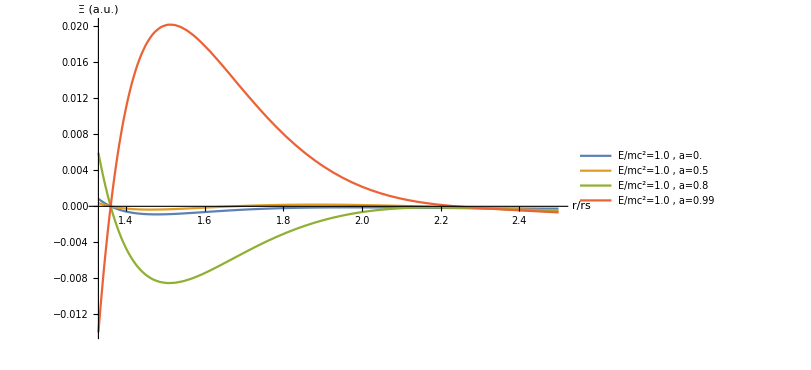

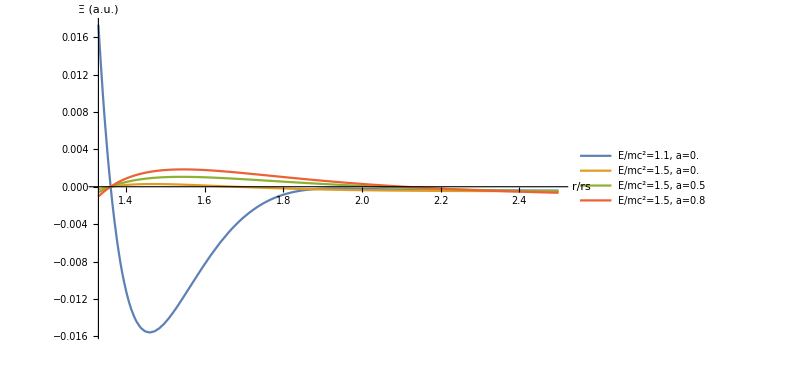

Show::gtype: Symbol is not a type of graphics.

Show[gammaofrJvariationplot1]

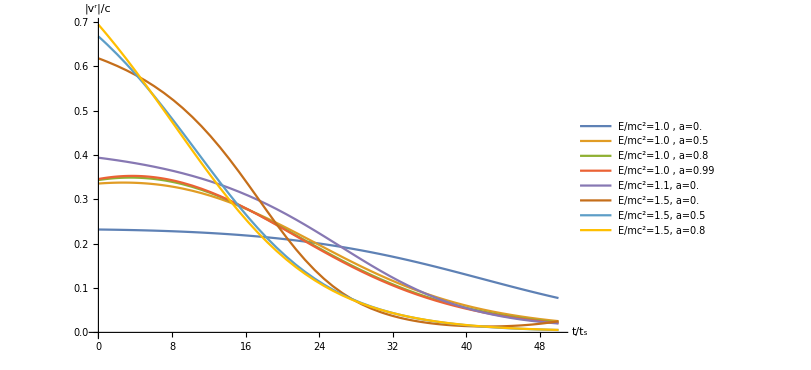

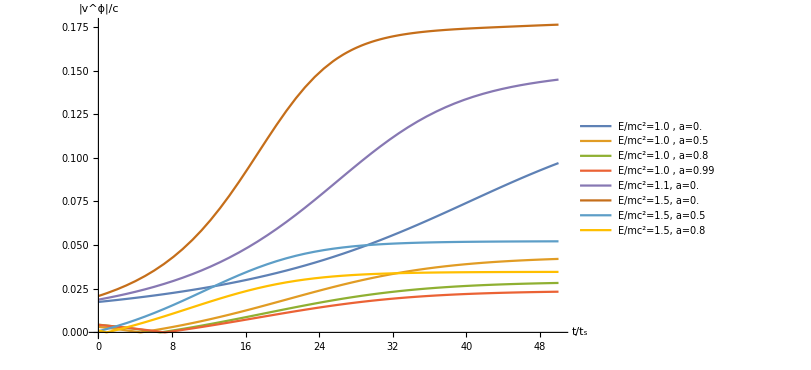

```mathematica
rmin=1.33;rmax=2.5;tplotmax=50;
vorticityJvariationplot1=Plot[{vorticitydata[[1]],vorticitydata[[2]],vorticitydata[[3]],vorticitydata[[4]]},{r,rmin,rmax},PlotLegends->legendJ,AxesLabel->{"r/rs","Ξ (a.u.)"},AxesOrigin->{rmin,Automatic},Evaluate@PlotOptions2,PlotRange->Full];
vorticityJvariationplot1=Show[vorticityJvariationplot1(*,Ticks->{TickScale[vorticityJvariationplot1,rs],Automatic}*)]
vorticityJvariationplot2=Plot[{vorticitydata[[5]],vorticitydata[[6]],vorticitydata[[7]],vorticitydata[[8]]},{r,rmin,rmax},PlotLegends->{legendJ[[5]],legendJ[[6]],legendJ[[7]],legendJ[[8]]},AxesLabel->{"r/rs","Ξ (a.u.)"},AxesOrigin->{rmin,Automatic},Evaluate@PlotOptions2,PlotRange->Full];
vorticityJvariationplot2=Show[vorticityJvariationplot2(*,Ticks->{TickScale[vorticityJvariationplot1,rs],Automatic}*)]
gammaofrJvariationplot2=Plot[{gammaofrdata[[1]],gammaofrdata[[2]],gammaofrdata[[3]],gammaofrdata[[4]],gammaofrdata[[5]],gammaofrdata[[6]],gammaofrdata[[7]],gammaofrdata[[8]]},{r,1.1,5},AxesOrigin->{0.95,0}, PlotLegends->legendJ,AxesLabel->{"r/rs","γ"},Evaluate@PlotOptions2];
gammaofrJvariationplot=Show[gammaofrJvariationplot1(*,Ticks->{TickScale[gammaofrJvariationplot1,rs],Automatic}*)]
rvelocityvectorJvariationplot=Plot[{rvelocityvectordata[[1]],rvelocityvectordata[[2]],rvelocityvectordata[[3]],rvelocityvectordata[[4]],rvelocityvectordata[[5]],rvelocityvectordata[[6]],rvelocityvectordata[[7]],rvelocityvectordata[[8]]},{t,0,tplotmax},PlotLegends->legendJ,AxesLabel->{"t/t_s","|v^r|/c"},Evaluate@PlotOptions2]
phivelocityvectorJvariationplot=Plot[{phivelocityvectordata[[1]],phivelocityvectordata[[2]],phivelocityvectordata[[3]],phivelocityvectordata[[4]],phivelocityvectordata[[5]],phivelocityvectordata[[6]],phivelocityvectordata[[7]],phivelocityvectordata[[8]]},{t,0,tplotmax},PlotLegends->legendJ,AxesLabel->{"t/t_s","|v^ϕ|/c"},Evaluate@PlotOptions2]
```

### Save Plots

```mathematica
Export[imagepath<>"vorticityJvariation1.pdf",vorticityJvariationplot1];
Export[imagepath<>"vorticityJvariation2.pdf",vorticityJvariationplot2];
Export[imagepath<>"gammaofrJvariation.pdf",gammaofrJvariationplot];
Export[imagepath<>"phivelocityvectorJvariation.pdf",phivelocityvectorJvariationplot];
Export[imagepath<>"rvelocityvectorJvariation.pdf",rvelocityvectorJvariationplot];
```

## Linear Studies

## 0th Order Flow

### Plot Options

```mathematica
PlotOptions31=Flatten[{PlotLabel->"",LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->22},ImageSize->500,
PlotLegends->
BarLegend
[
20,
LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->22},
LegendLayout->"Column",
LegendLabel->
Style[
"v^ϕ/c",25,
FontFamily->"Latin Modern Roman"
]
],
ColorFunction->"TemperatureMap",Contours->15,PlotPoints->30, ClippingStyle->Automatic,
FrameTicks->{{Table[{y,ToString[Round[10^y,0.001]]},{y,Log[10,0.001],Log[10,10000]}],None},{Table[{x,ToString[Round[10^x,0.001]]},{x,Log[10,0.01],Log[10,10000]}],None}}}];
PlotOptions311=Flatten[{Frame->True,PlotLabel->"",LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->20},FrameLabel->{Style["r/r_s",25],Style["v/c",25]},ImageSize->600,AxesOrigin->{1,0},PlotLegends->{"T_0=0.1","T_0=1","T_0=10","T_0=100"}}];
```

### Velocity Equation

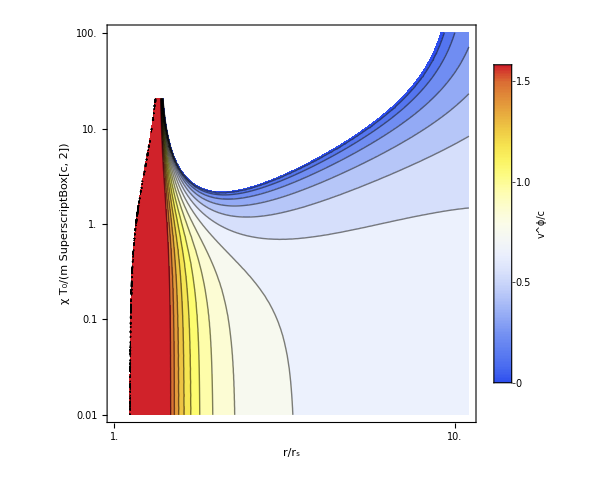
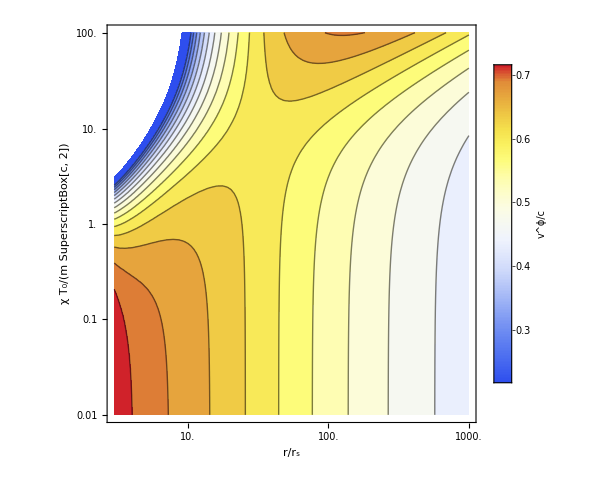
-Graphics- | -Graphics-

```mathematica
rs1=1;
α1[r_]=√(1-rs1/r);

γ1[r_]=1/(√(α1[r]^2-u1[r]^2 r^2));
t1[r_]=T0((1-√(rs1/r))/r^3)^(1/4);
f1[r_]=BesselK[3,B1/t1[r]]/BesselK[2,B1/t1[r]];
f11[tt1_]=BesselK[3,B1/tt1]/BesselK[2,B1/tt1];
AA1[r_]=(A1+(f11'[tt1]/.tt1->t1[r])/(f11[tt1]/.tt1->t1[r]))t1'[r]r;
eq11[r_,A_]=√(rs1/(2 r)((1+2A)/(1-A))-A/(1-A));
vphiplot=Grid[{
{uphiplot21=ContourPlot[eq11[r,AA1[10^r]/.A1->10^χ01/.T0->1/.B1->1],{r,Log10[1],Log10[11]},{χ01,Log10[0.01],Log10[101]},Evaluate@PlotOptions31,FrameLabel->{Style["r/r_s",25],Style["χ T_0/(m SuperscriptBox[c, 2])",25]}],
uphiplot22=ContourPlot[eq11[r,AA1[10^r]/.A1->10^χ01/.T0->1/.B1->1],{r,Log10[3],Log10[1001]},{χ01,Log10[0.01],Log10[101]},Evaluate@PlotOptions31,FrameLabel->{Style["r/r_s",25],Style["χ T_0/(m SuperscriptBox[c, 2])",25]}]}}]
Export[imagepath<>"vphiplot.pdf",uphiplot22];
```

## Growth Rate B(ϕ)

### Plot Options

```mathematica
PlotOptions3=Flatten[{PlotLabel->"",LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->22},FrameLabel->{Style["r/r_s",25],Style["k_ϕ",25]},ImageSize->400,
PlotLegends->
BarLegend
[
20,
LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->22},
LegendLayout->"Column",
LegendLabel->
Style[
"ν r_s/c",25,
FontFamily->"Latin Modern Roman"
]
],
ColorFunction->"TemperatureMap",Contours->15,PlotPoints->30, ClippingStyle->Automatic}];
PlotOptions4=Flatten[{Frame->True,PlotLabel->"",LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->20},FrameLabel->{Style["r/r_s",25],Style["ν r_s/c",25]},ImageSize->600,PlotLegends->{"n=0","n=1","n=2","n=3"}}];
```

### Growth Rate Plot

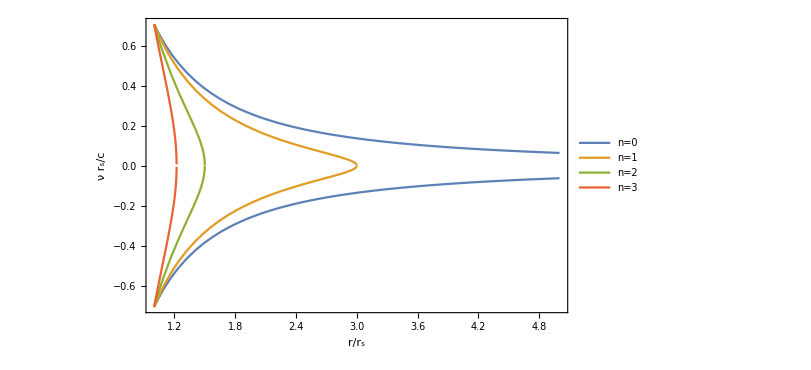

```mathematica
α1[r_]=√(1-rs1/r);
der[r_]=(D[α1[x]D[x α1[x],x],x]/x)/.x->r;
eq1[r_,rs1_,k1_]=ν^2-der[r]+α1[r]^2/r^2 k1^2;
sol1[r_,rs1_,k1_]=rs1* ν/.Solve[eq1[r,rs1,k1]==0,ν];
linearplot1=Plot[{sol1[r,1,0],sol1[r,1,1/2],sol1[r,1,2/2],sol1[r,1,3/2]},{r,1,5},Evaluate@PlotOptions4]
Export[imagepath<>"linearplot1.pdf",linearplot1];
```

## MRI vs MagnetoFluid Comparison B(ϕ)

#### Plot Options

```mathematica
PlotOptions312=Flatten[{Frame->True,PlotLabel->"",LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->20},FrameLabel->{Style["r/r_s",25],Style["(ν r_s/c)^2",25]},ImageSize->500,PlotLegends->{"Magnetofluid","MRI"},PlotStyle->Thickness[0.01],AxesOrigin->{0.95,0}}];
```

#### Comparison

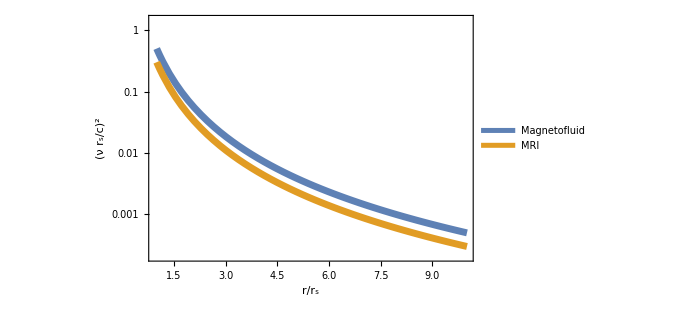

```mathematica
grMRI[r_,rs1_]=0.3(rs1/r)^3;
grMF[r_,rs1_]=Simplify[sol1[r,rs1,0]^2];
mrimfcompplot1=LogPlot[{grMF[r,1],grMRI[r,1]},{r,1,10},Evaluate@PlotOptions312]
(*mrimfcompplot2=Plot[{grMRI[r,1],grMF[r,1]},{r,1,3},Evaluate@PlotOptions312];
mrimfcompplot=Grid[{{mrimfcompplot1,mrimfcompplot2}}]*)
Export[imagepath<>"mrimfcomp.pdf",mrimfcompplot1];
```

## Growth Rate B(r), u_1^θ(r)

```mathematica
α1[r_]=√(1-rs/r);
```

#### Plot Options

```mathematica
PlotOptions3=Flatten[{PlotLabel->"",LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->22},ImageSize->400,FrameLabel->{Style["r/r_s",25],Style["Im(u_1^θ)",25]},
ColorFunction->"TemperatureMap",Contours->15,PlotPoints->30, ClippingStyle->Automatic}];
PlotOptions4=Flatten[{Frame->True,PlotLabel->"",LabelStyle->{FontFamily->"Latin Modern Roman",FontSize->20},ImageSize->400,PlotRange->All}];
```

#### Eigenfunctions (a=b to be zero at infinity) u_1^θ(r)

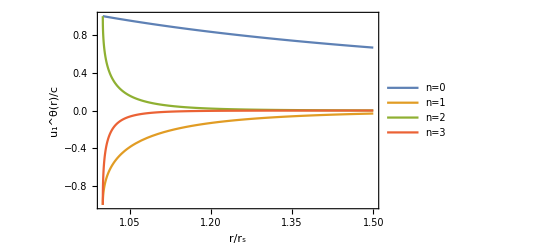

```mathematica
sol1=DSolve[{F''[x]+α1'[x]/α1[x] F'[x]-ν^2/α1[x]^2 F[x]==0},F[x],x][[1]];
u1theta[x_,ν_,aa_,bb_]=F[x]/x/.sol1/.rs->1/.c->1/.C[1]->aa/.C[2]->I bb;
u1thetaofrplot=Plot[{Re[u1theta[x,0,1,1]],Re[u1theta[x,2,1,1]],Re[u1theta[x,4,1,1]],Re[u1theta[x,6,1,1]]},{x,1,1.5},PlotLegends->{"n=0","n=1","n=2","n=3"},Evaluate@PlotOptions4,FrameLabel->{Style["r/r_s",25],Style["u_1^θ(r)/c",25]}]
Export[imagepath<>"u1thetaofr.pdf",u1thetaofrplot];
```

#### Eigenfunctions (b=- 2 a ν to be zero at infinity) B_1^θ(r)

```mathematica
(*
rs=1;
c=1;
sol2=DSolve[{G''[x]+3 α'[x]/α[x] G'[x]-(ν^2/α[x]^2-(α'[x]/α[x])^2-α''[x]/α[x])G[x]==0},G[x],x]
*)
B1phi[x_,ν_,aa_,rs_]:=aa/x((ⅇ^(√x √(-rs+x) ν) √x (√x+√(-rs+x))^(rs ν))/(√(-rs+x))-2ν (ⅇ^(√x √(-rs+x) ν) √x (√x+√(-rs+x))^(rs ν)  NIntegrate[(ⅇ^(-2 ν √t √(-rs+t)) √t (√t+√(-rs+t))^(-2 rs ν))/(√(-rs+t)),{t,1,x}])/(√(-rs+x)))
```

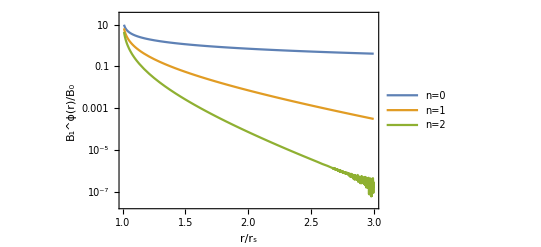

```mathematica
biphiofrplot=LogPlot[{B1phi[x,0,1,1],B1phi[x,2,1,1],B1phi[x,4,1,1]},{x,1.01,3},PlotLegends->{"n=0","n=1","n=2"},Evaluate@PlotOptions4,FrameLabel->{Style["r/r_s",25],Style["B_1^ϕ(r)/B_0",25]}]
Export[imagepath<>"B1phiofr.pdf",biphiofrplot];
```

#### Proof that ν=2n

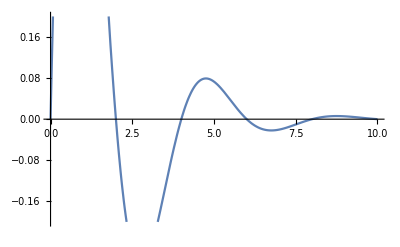

```mathematica
numax=10;
u1max=0.2;
Plot[Im[u1theta[1.1,ν,2,2]],{ν,0,numax},PlotRange->{{0,numax},{-u1max,u1max}}]
```

## Other Calculations

```mathematica
α[r]=√(1-1/r);
aa[r_,ν_,k_]=(r ν)/(α[r] k);
LHS[r_,ν_]=(ν^2 F[r])/α[r];
RHS1[r_,ν_]=D[α[r]F'[r],r];
RHS2[r_,ν_,k_]=D[(α[r]F'[r])/(1+aa[r,ν,k]^2),r];
rmin=1.1;
rmax=30;
Frmax=0.001;
Fprmax=-0.01;
Frmin=1;
Fprmin=-1;
sol1[ν_]=DSolve[{Simplify[LHS[r,ν]-RHS1[r,ν]]==0,F[rmax]==Frmax,F'[rmax]==Fprmax},F[r],{r}][[1]];
f1[rr_,ν_]=F[r]/.sol1[ν]/.r->rr;
sol2[ν_,k_]:=NDSolve[{Simplify[LHS[r,ν]-RHS1[r,ν]+RHS2[r,ν,k]]==0,F[rmax]==Frmax,F'[rmax]==Fprmax},F[r],{r,rmin,rmax}][[1]]
f2[rr_,ν_,k_]:=F[r]/.sol2[ν,k]/.r->rr;
```

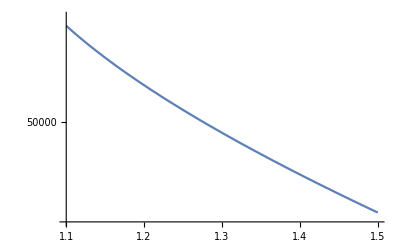

```mathematica
LogPlot[{f2[rr,0.5,0.001]},{rr,rmin,rmax}]
```

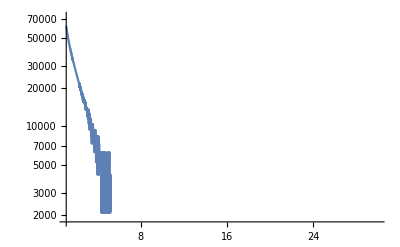

```mathematica
LogPlot[{f1[rr,0.5]},{rr,rmin,rmax}]
```

```mathematica
1- 1. Coth[31 ν]^2/.ν->0.1
```

-0.00815077

```mathematica
Length[sols[rr][[All,1]]]
```

10

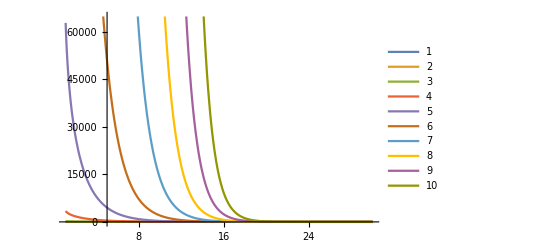

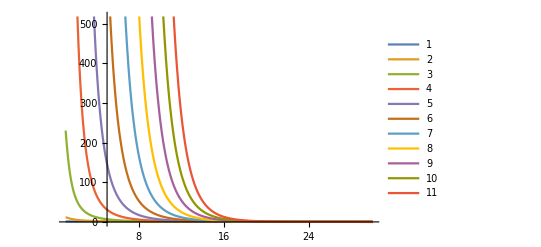

```mathematica
Plot[{Evaluate[sols[rr][[All,1]]]},{rr,rmin,rmax},PlotLegends->Automatic,PlotRange->{{rmin,rmax},{0,Automatic}}]
Plot[{Evaluate[sols[rr][[1,All]]]},{rr,rmin,rmax},PlotLegends->Automatic]
```

```mathematica
fsol[r_,ν_,A_]=F[r]/.sol1/.C[1]->A/.C[2]->I A
```

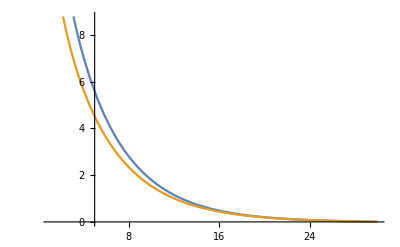

```mathematica
Plot[{f1[rr,0.21],sols[rr][[2,1]]},{rr,rmin,rmax}]
```

```mathematica
fsol[r,0,1]/(α[r]r)/.r->10
```

1/(3 √10)

```mathematica
e=1.6 10^-19;
me=9.1 10^-31;
G=6.7 10^-11;
c=3 10^8;
Msun=2 10^30;
rs=(2 G Msun)/c^2;

β0=(e^2 rs^2)/(me c^2)
```

2.77166×10^-18

```mathematica
1/β0
```

3.60794×10^17

```mathematica
α[r_]=√(1-1/r);
Expr[r_]:=F''[r]+α'[r]/α[r] F'[r]-ν^2/α[r]^2 F[r];
sol=DSolve[{Expr[r]==0,F[1]==0},F[r],r];
B[r_]=(F[r]/.sol[[1]]/.C[2]->-I)/(α[r]r)
```

Sinh[(ν (-√r+r^(3/2)+√(-1+r) Log[√(-1+r)+√r]))/(√(-1+r))]/(√(1-1/r) r)

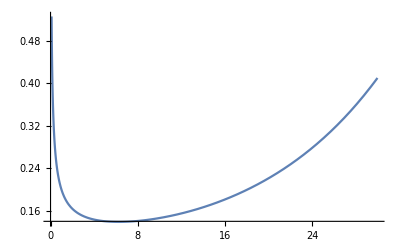

```mathematica
Plot[B[r]/.ν->0.1,{r,0,30}]
```

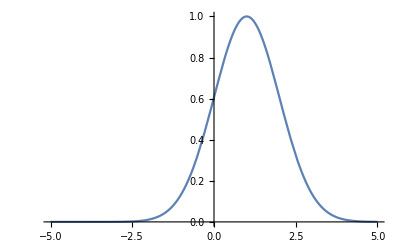

```mathematica
Plot[Exp[(-(v-1)^2)/2],{v,-5,5},PlotRange->{Automatic,{0,1}}]
```